```mathematica
NotebookSave[]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
rmax[v_,δ_,m_,omega_]=N[(√δ v^2)/(2 √(m^2-δ v^4)(omega-√(m^2-δ v^4)))];
ωmin[v_,δ_,m_]=N[√(m^2-δ v^4)];
```

```mathematica
Expand[(δ(z-v^2)^2+m^2-δ v^4)z]
```

```mathematica
Clear[ω]
```

```mathematica
ρ=12.01;
sol=ParametricNDSolve[{y''[r]+2/r y'[r]+ω^2 y[r]==(1-4 δ v^2 y[r]^2+3δ y[r]^4)y[r],y[10^-2]==y0-10^-4/6(ω^2 y0-(1-4 δ v^2 y0^2+3δ y0^4)y0),y'[ρ]==-(√(1-ω^2)+1/ρ)y[ρ]},y,{r,10^-2,ρ},{δ,v,ω,y0},WorkingPrecision->MachinePrecision(*,Method->"ImplicitRungeKutta"*)]
```

{y→ParametricFunction[<>]}

```mathematica
ρ=12.01;ϵ=10^-2;
sol2=ParametricNDSolve[{y''[r]+2/r y'[r]+ω^2 y[r]==(1-4 δ v^2 y[r]^2+3δ y[r]^4)y[r],y''[ϵ]==1/3(1-ω^2-4 δ v^2 y[ϵ]^2+3δ y[ϵ]^4)y[ϵ],y'[ρ]==-(√(1-ω^2)+1/ρ)y[ρ]},y,{r,ϵ,ρ},{δ,v,ω},WorkingPrecision->MachinePrecision(*,Method->"ImplicitRungeKutta"*)]
```

{y→ParametricFunction[<>]}

```mathematica
Plot[y[0.6,1,0.92][r]/.sol2,{r,0.1,6}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::nlnum1: The function value {0.+NDSolve`y$104$1'[1/100],0.} is not a list of numbers with dimensions {2} when the arguments are {0.,0.,0.,0.}.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NDSolve::nlnum1: The function value {0.+NDSolve`y$105$1'[1/100],0.} is not a list of numbers with dimensions {2} when the arguments are {0.,0.,0.,0.}.

NDSolve::nlnum1: The function value {0.+NDSolve`y$106$1'[1/100],0.} is not a list of numbers with dimensions {2} when the arguments are {0.,0.,0.,0.}.

General::stop: Further output of NDSolve::nlnum1 will be suppressed during this calculation.

-Graphics-

```mathematica
ListLinePlot[Table[{0.8+0.001i,Log[((y[0.6,1,0.93,0.8+0.001i][0.01+2 10^-2]-y[0.6,1,0.93,0.8+0.001i][0.01])/(2 10^-2))^2]/.sol},{i,0,100}]]
```

```mathematica
FindMinimum[Log[((y[0.6,1,ω,y0][0.01+2 10^-2]-y[0.6,1,ω,y0][0.01])/(2 10^-2))^2]/.ω->0.93/.sol,{y0,0.88}]
```

```mathematica
f[x_]:=y[0.6,1,0.93,0.8755167076959837][x+0.01]/.sol;
```

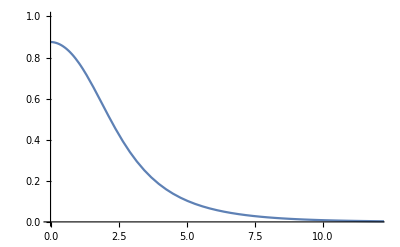

```mathematica
Plot[f[x],{x,0,13},PlotRange->{{0,12},{0,1}}]
```

```mathematica
QBsinglemode[v_,δ_,ω_,R_,n_]:=(
h=R/n;
a=0;
a1[x_]:=1;
a2[x_]:=2/x;
a3[x_]:=ω^2;
S[y_]:=(1-4 δ v^2 y^2+3δ y^4)y;
eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
Table[iceq[i]=1/6 cc[i-1]+2/3 cc[i]+1/6 cc[i+1]==f[i h],{i,0,n}];
iceq[-1]=cc[-1]==cc[1]; iceq[n+1]=cc[n-1]==cc[n+1];
approx=Table[cc[j],{j,-1,n+1}]/.NSolve[Table[iceq[i],{i,-1,n+1}],Table[cc[j],{j,-1,n+1}]];
coef=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],approx[[1,1+k]]},{k,0,n+1}](*,WorkingPrecision->100*)];
For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
fin[x_]:=Sum[t[i]BSplineBasis[{3,{a+(i-2)h,a+(i-1)h,a+i h,a+(i+1)h,a+(i+2)h}},0,x],{i,-1,n+1}];
ϕin=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
)
```

```mathematica
QBsinglemode[1,0.6,0.7,12,400]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

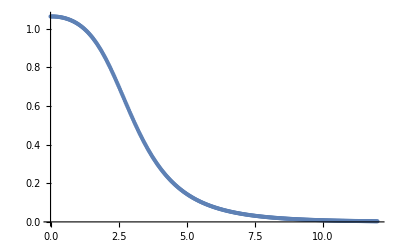

```mathematica
ListPlot[ϕin]
```

```mathematica
rmax[1,0.6,1,0.7]
```

9.06621

```mathematica
f[x]:=1/2(1-Tanh[(x-9.06)])
```

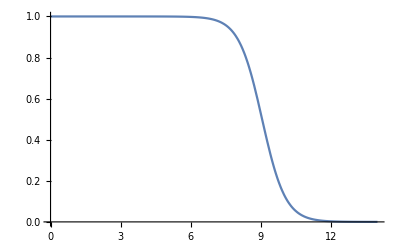

```mathematica
Plot[f[x],{x,0,14}]
```

```mathematica
rmax[1,0.6,1,0.655]
```

27.1629

```mathematica
QB[v_,δ_,omega_,α_,L_,n_,Ω_]:=(
R=L;
ω=omega;
h=R/n;
a=0;
a1[x_]:=1;
a2[x_]:=2/x;
a3[x_]:=ω^2;
S[y_]:=(1-4 δ v^2 y^2+3δ y^4)y;
V[y_]:=y^2-2 δ v^2 y^4+δ y^6;
eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
Table[iceq[i]=1/6 cc[i-1]+2/3 cc[i]+1/6 cc[i+1]==y[0.6,1,0.93,0.8755167076959837][0.01+i h]/.sol,{i,0,n}];
iceq[-1]=cc[-1]==cc[1]; iceq[n+1]=cc[n-1]==cc[n+1];
approx=Table[cc[j],{j,-1,n+1}]/.NSolve[Table[iceq[i],{i,-1,n+1}],Table[cc[j],{j,-1,n+1}]];
coef=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],approx[[1,1+k]]},{k,0,n+1}](*,WorkingPrecision->100*)];
For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
y[x_]:=Sum[t[i]BSplineBasis[{3,{a+(i-2)h,a+(i-1)h,a+i h,a+(i+1)h,a+(i+2)h}},0,x],{i,-1,n+1}];
coefficients[0]=Table[{h i,t[i]},{i,-1,n+1}];
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
Q[0]=2 ω 4 π Sum[(h (i-1))^2 ϕ[[i,2]]^2,{i,1,n+1}];
H[0]=4 π Sum[(h (i-1))^2(((ϕ[[i+1,2]]-ϕ[[i-1,2]])/(2h))^2+ω^2 ϕ[[i,2]]^2+V[ϕ[[i,2]]]),{i,2,n}];
w[0]=ω;
dx[0]=h;
Clear[a3];
For[k=1,k≤Ω,k++,
ω=omega-0.002 k;
time=1;
While[ϕ[[time,2]]/ϕ[[1,2]]>10^-2,time++];
R=1.5(time-1)h;
h=R/n;
a3[x_]:=ω^2;
eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[a+i h],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[a+i h],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
Table[iceq[i]=1/6 cc[i-1]+2/3 cc[i]+1/6 cc[i+1]==y[i h],{i,0,n}];
iceq[-1]=cc[-1]==cc[1]; iceq[n+1]=cc[n-1]==cc[n+1];
approx=Table[cc[j],{j,-1,n+1}]/.NSolve[Table[iceq[i],{i,-1,n+1}],Table[cc[j],{j,-1,n+1}]];
coef=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],approx[[1,1+k]]},{k,0,n+1}](*,WorkingPrecision->100*)];
For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*profile[k]=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];*)
coefficients[k]=Table[{h i,t[i]},{i,-1,n+1}];
Q[k]=2 ω 4 π Sum[(h (i-1))^2 ϕ[[i,2]]^2,{i,1,n+1}];
H[k]=4 π Sum[(h (i-1))^2(((ϕ[[i+1,2]]-ϕ[[i-1,2]])/(2h))^2+ω^2 ϕ[[i,2]]^2+V[ϕ[[i,2]]]),{i,2,n}];
w[k]=ω;
dx[k]=h;
y[x_]:=Sum[t[i]BSplineBasis[{3,{a+(i-2)h,a+(i-1)h,a+i h,a+(i+1)h,a+(i+2)h}},0,x],{i,-1,n+1}];
Clear[a3];
];
)
```

QB[ v, δ, ω, α, L, n , Ω]

```mathematica
QB[1,0.6,0.92,1,12,300,10]
```

```mathematica
coefficients[1][[2]]
```

{0.,0.91919}

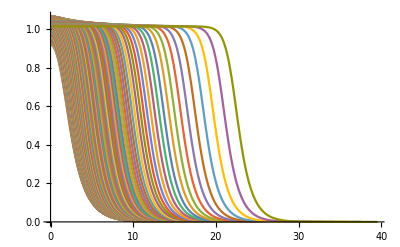

```mathematica
ListLinePlot[Table[profile[i],{i,1,130}],PlotRange->Full]
```

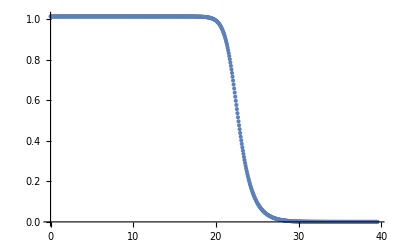

```mathematica
ListPlot[profile[130]]
```

```mathematica
{ϕ[[11,2]],ω}
```

{1.01413,0.66}

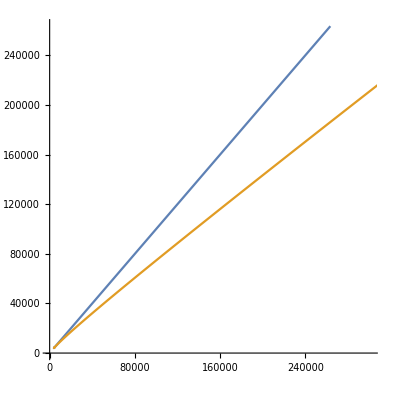

```mathematica
ListLinePlot[{Table[{Q[k],Q[k]},{k,0,133}],Table[{Q[k],H[k]},{k,0,133}]},AspectRatio->1]
```

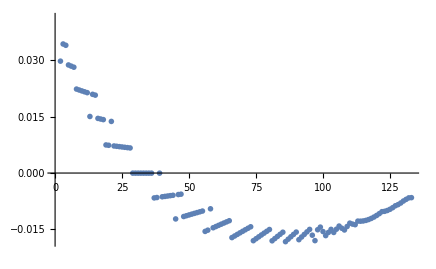

```mathematica
ListPlot[Table[((H[k+1]-H[k-1])/(Q[k+1]-Q[k-1])-1/4(w[k+1]+w[k-1]+2w[k]))/w[k],{k,1,133}]]
```

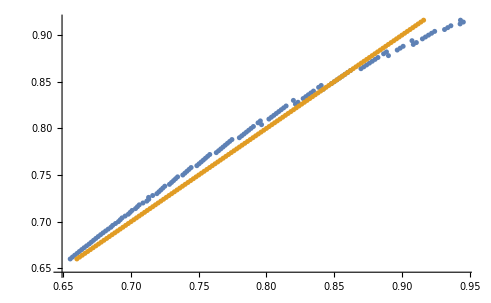

```mathematica
ListPlot[{Table[{(H[k+1]-H[k-1])/(Q[k+1]-Q[k-1]),1/4(w[k+1]+w[k-1]+2w[k])},{k,2,130}],Table[{w[k],w[k]},{k,2,130}]}]
```

```mathematica
f[r_]:=y[0.6,1,0.93,0.8755167076959837][r+0.01]/.sol;
```

```mathematica
QBfull[v_,δ_,omega_,dω_,L_,n_,Ωin_,Ωout_]:=(
R=L;
ω=omega;
h=R/n;
a=0;
a1[x_]:=1;
a2[x_]:=2/x;
a3[ω_]:=ω^2;
S[y_]:=(1-4 δ v^2 y^2+3δ y^4)y;
V[y_]:=y^2-2 δ v^2 y^4+δ y^6;
(*MAIN CYCLE*)
For[k=Ωin,k≤Ωout,k++,
eq[0]=(2/3 a3[0] h^2-6)c[0]+(6+(a3[0] h^2)/3) c[1]==h^2 S[2/3 c[0]+1/3 c[1]];
Table[p[i]=6 a1[a+i h]-3h a2[a+i h]+h^2 a3[ω],{i,1,n}];
Table[q[i]=-12 a1[a+i h]+4 h^2 a3[ω],{i,1,n}];
Table[r[i]=6 a1[a+i h]+3h a2[a+i h]+h^2 a3[ω],{i,1,n}];
Table[eq[i]=p[i]c[i-1]+q[i]c[i]+r[i]c[i+1]==6 h^2 S[1/6 c[i-1]+2/3 c[i]+1/6 c[i+1]],{i,1,n}];
eq[n+1]=(1/6(√(1-ω^2)+1/R)-1/(2h))c[n-1]+2/3(√(1-ω^2)+1/R)c[n]+(1/6(√(1-ω^2)+1/R)+1/(2 h))c[n+1]==0;
Table[iceq[i]=1/6 cc[i-1]+2/3 cc[i]+1/6 cc[i+1]==f[i h],{i,0,n}];
iceq[-1]=cc[-1]==cc[1]; iceq[n+1]=cc[n-1]==cc[n+1];
approx=Table[cc[j],{j,-1,n+1}]/.NSolve[Table[iceq[i],{i,-1,n+1}],Table[cc[j],{j,-1,n+1}]];
coef=Table[c[k],{k,0,n+1}]/.FindRoot[Table[eq[i],{i,0,n+1}],Table[{c[k],approx[[1,1+k]]},{k,0,n+1}](*,WorkingPrecision->100*)];
For[i=0,i≤n+1,i++,t[i]=coef[[i+1]]];
t[-1]=t[1];
ϕ=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];
(*profile[k]=Table[{h i,1/6 t[i-1]+2/3 t[i]+1/6 t[i+1]},{i,0,n}];*)
coefficients[k]=Table[{h i,t[i]},{i,-1,n+1}];
Q[k]=2 ω 4 π Sum[(h (i-1))^2 ϕ[[i,2]]^2,{i,1,n+1}];
H[k]=4 π Sum[(h (i-1))^2(((ϕ[[i+1,2]]-ϕ[[i-1,2]])/(2h))^2+ω^2 ϕ[[i,2]]^2+V[ϕ[[i,2]]]),{i,2,n}];
w[k]=ω;
dx[k]=h;
f[x_]:=Sum[t[i]BSplineBasis[{3,{a+(i-2)h,a+(i-1)h,a+i h,a+(i+1)h,a+(i+2)h}},0,x],{i,-1,n+1}];
(*Values for next iterration*)
ω=omega-dω (k-Ωin+1);
time=1;
While[ϕ[[time,2]]/ϕ[[1,2]]>10^-2,time++];
R=1.5(time-1)h;
box[k]=R;
h=R/n;
];
)
```

```mathematica
QBfull[1,0.6,0.649,0.0002,63.31370811533436,400,205,235]
```

```mathematica
rmax[1,0.6,1,0.65]
```

34.904

```mathematica
{w[n],box[n]}/.n->205
```

{0.649,64.1051}

```mathematica
ωmin[1,0.6,1]
```

0.632456

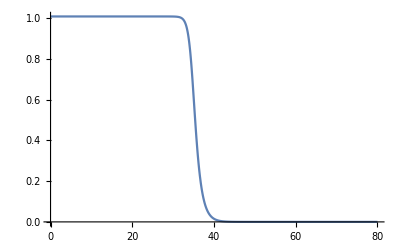

```mathematica
Plot[f2[x],{x,0,80},PlotRange->Full]
```

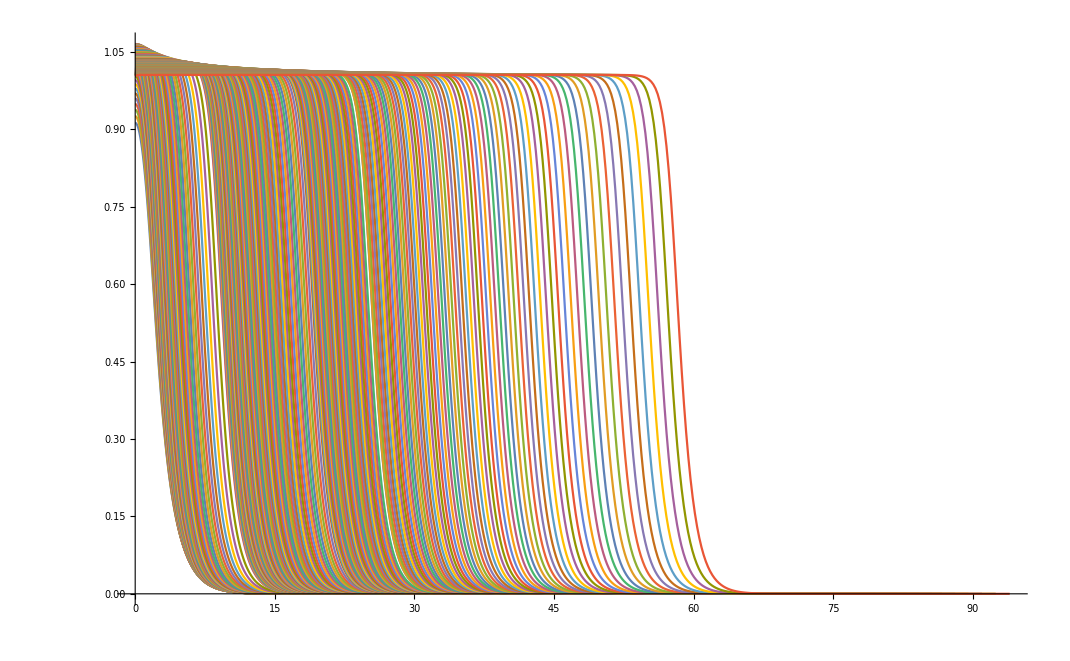

```mathematica
ListLinePlot[Table[Table[{coefficients[k][[i+1,1]],1/6(coefficients[k][[i,2]]+4coefficients[k][[i+1,2]]+coefficients[k][[i+2,2]])},{i,1,401}],{k,0,235,1}],PlotRange->Full]
```

```mathematica
f2[x_]:=Sum[coefficients[200][[i+2,2]]BSplineBasis[{3,{a+(i-2)dx[200],a+(i-1)dx[200],a+i dx[200],a+(i+1)dx[200],a+(i+2)dx[200]}},0,x],{i,-1,400+1}];
```

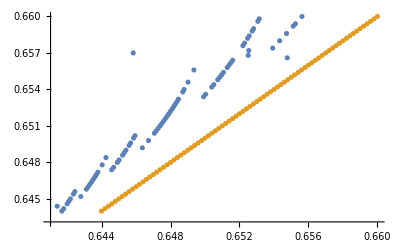

```mathematica
ListPlot[{Table[{(H[k+1]-H[k-1])/(Q[k+1]-Q[k-1]),w[k]},{k,150,230}],Table[{w[k],w[k]},{k,150,230}]},PlotRange->Full]
```

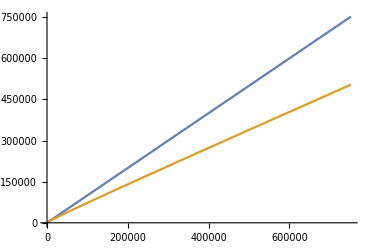

```mathematica
ListLinePlot[{Table[{Q[k],Q[k]},{k,0,165}],Table[{Q[k],H[k]},{k,0,165}]},AspectRatio->2/3]
```

```mathematica
(0.216-0.2)/0.2
```

0.08

```mathematica
(0.65^2-ωmin[1,0.6,1]^2)/ωmin[1,0.6,1]^2
```

0.05625